```mathematica
rawdata=Import["/Users/stevenschowalter/Desktop/phys191mms/Rb Data/423fstep7.txt.txt","Data"];
```

```mathematica
num=Dimensions[rawdata][[1]]
```

161

```mathematica
freq=Take[rawdata,All,{1}];
signal=Take[rawdata,All,{2}];
```

```mathematica
plotdata=Take[rawdata,All,2];
```

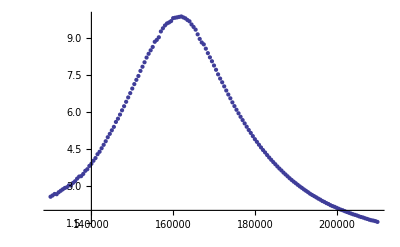

```mathematica
dataplot=ListPlot[plotdata]
```

```mathematica
Do[If[Max[signal]==signal[[i]][[1]],{Print[i,plotdata[[i]]],{max}=freq[[i]]}],{i,1,num}]
```

65{162000.,9.892}

```mathematica
model=g/(π (g^2+(x-x0)^2/b));
```

```mathematica
Needs["NonlinearRegression`"]
```

```mathematica
fitdata=NonlinearRegress[Take[plotdata,{1,161}],model,{x0,g,b},x]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.00937159, 101.624, 1.36801×10^-11}, « 1 », {0., 0., -2.37768×10^-10}} may contain significant numerical errors.

{BestFitParameters→{x0→161743.,g→0.0328031,b→3.23693×10^11},ParameterCITable→ | Estimate | Asymptotic SE | CI
x0 | 161743. | 61.728 | {161621.,161865.}
g | 0.0328031 | 0.000109567 | {0.0325867,0.0330195}
b | 3.23693×10^11 | 2.42821×10^9 | {3.18897×10^11,3.28489×10^11},EstimatedVariance→0.0290049,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 3 | 5301.16 | 1767.05
Error | 158 | 4.58277 | 0.0290049
Uncorrected Total | 161 | 5305.74 | 
Corrected Total | 160 | 1143.24 | ,AsymptoticCorrelationMatrix→(1. | -0.0261875 | -0.0597482
-0.0261875 | 1. | 0.120854
-0.0597482 | 0.120854 | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 0.00848228
Max Parameter-Effects | 0.0156373
95. % Confidence Region | 0.612929}

```mathematica
fit=model/.fitdata[[1]][[2]];
```

```mathematica
fitplot=Plot[fit,{x,100000,200000},PlotStyle->{Red, Thick}];
```

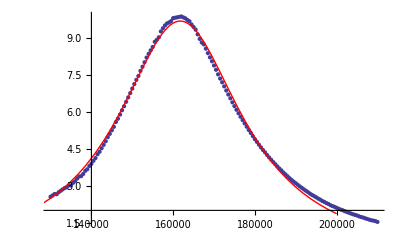

```mathematica
Show[dataplot,fitplot]
```